```mathematica
gtt[r_]:=-1+(1+r a1+r^2 a2+r^3 a3+r^4 a4+r^5 a5+r^6 a6)/(a7+r a8+r^2 a9+r^3 a10+r^4 a11+r^5 a12+r^6 a13+r^7 a14)
```

```mathematica
grr[r_]:=1-(r b1+r^2 b2+r^3 b3+r^4 b4+r^5 b5+r^6 b6)/(b7+r b8+r^2 b9+r^3 b10+r^4 b11+r^5 b12+r^6 b13+r^7 b14)
```

```mathematica
gθθ[r_]:=r^2
```

```mathematica
gϕϕ[r_]:=r^2                            (*We restrict to the equatorial plane θ=π/2 *)
```

```mathematica
D[gtt[r],r]
```

-(((a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2)+(a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)

```mathematica
gttr[r_]:=-(((a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2)+(a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)
```

```mathematica
D[gttr[r],r]
```

```mathematica
gttrr[r_]:=(2 (a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6)^2 (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^3-(2 (a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5) (a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2-((2 a9+6 a10 r+12 a11 r^2+20 a12 r^3+30 a13 r^4+42 a14 r^5) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2+(2 a2+6 a3 r+12 a4 r^2+20 a5 r^3+30 a6 r^4)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)
```

```mathematica
gϕϕr[r_]:= 2*r
```

```mathematica
gϕϕrr[r_]:= 2
```

```mathematica
Ω[r_]:= Sqrt[(-gttr[r])/gϕϕr[r]]

Ω[r]





(*Joaquin, a continuación, denotada Ω, esta la expresión para la velocidad angular*)
```

```mathematica
Ω:=1/(√2)(√(-1/r(-(((a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2)+(a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7))))
```

```mathematica
Ωr[r_]:=(-1/r((2 (a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6)^2 (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^3-(2 (a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5) (a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2-((2 a9+6 a10 r+12 a11 r^2+20 a12 r^3+30 a13 r^4+42 a14 r^5) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2+(2 a2+6 a3 r+12 a4 r^2+20 a5 r^3+30 a6 r^4)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7))+1/r^2(-(((a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2)+(a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)))/(2 √2 √(-1/r(-(((a8+2 a9 r+3 a10 r^2+4 a11 r^3+5 a12 r^4+6 a13 r^5+7 a14 r^6) (1+a1 r+a2 r^2+a3 r^3+a4 r^4+a5 r^5+a6 r^6))/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7)^2)+(a1+2 a2 r+3 a3 r^2+4 a4 r^3+5 a5 r^4+6 a6 r^5)/(a7+a8 r+a9 r^2+a10 r^3+a11 r^4+a12 r^5+a13 r^6+a14 r^7))))
```

```mathematica
Ωrn[r_]:= -1/2*1/Sqrt[-gttr[r]*gϕϕr[r]]*(gttrr[r]+gϕϕrr[r]*(Ω[r])^2)
```

```mathematica
Den[r_]:= Sqrt[-gtt[r]-(Ω[r])^2*gϕϕ[r]]



int[r_]:= gϕϕr[r]*Ω[r]+gϕϕ[r]*Ωr[r]-1/2*(gϕϕ[r]*Ω[r])^2/(gϕϕr[r]*(Den[r])^2)*(gttrr[r]+gϕϕrr[r]*(Ω[r])^2)

det[r_]:= Sqrt[-gtt[r]*grr[r]*gϕϕ[r]]


f[r_]:=- Ωr[r]/(det[r]*(Den[r])^2)
```

```mathematica
a1:=-0.12835651132329287

a2:=0.013682816437869968

a3:=-0.0000481174714805307
a4:=0.00005645401289538938
a5:=-4.950385183447073*^-6
a6:=1.2257668397193955*^-6
a7:=2.234495931121217
a8:=-0.286705001384064
a9:=0.0535085065184157
a10:=-0.002796436948776261
a11:=0.00043953642633610485
a12:=0.000015216185242475638
a13:=-2.2791584430232886*^-6
a14:=6.116664949485882*^-7
b1:=0.002169200852262319
b2:=-0.19546743355115126
b3:=0.06287130575728342
b4:=-0.010651955590611452
b5:=0.0009203500154294379
b6:=-0.00003751481658539803
b7:=13.99470385461245
b8:=-3.910737098471579
b9:=0.3926444282051113
b10:=0.1007509282796355
b11:=-0.03817380739469051
b12:=0.00609572731408874
b13:=-0.0004946554674560391
b14:=0.000018733095859225056
```

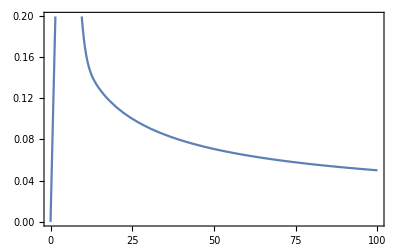

```mathematica
Plot[int[r],{r,0,100},Frame->True]
```

```mathematica
NIntegrate[int[r],{r,9.89994,100}]
```

6.87348

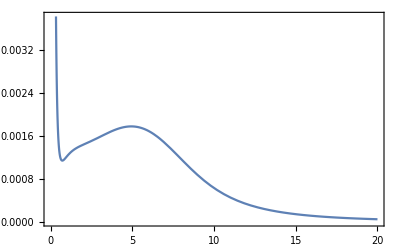

```mathematica
Plot[f[r],{r,0,20},Frame->True]
```

```mathematica
1/(Den[0.1])^2
```

1.81004

```mathematica
Limit[Ωr[r],r->0]
```

Indeterminate

```mathematica
rmin:= 9.89994



fi[x_]:= NIntegrate[int[r],{r,rmin,x}]
fi[9.89994,9.89994]
```

fi[9.89994,9.89994]

0.

```mathematica
(*Units*)

c:= 3*10^10       (*speed of light*)
Msun:= 1.989*10^(33)    (*mass of the Sun in grams*)
yr:= 365*24*60*60     (*seconds in one year*)
G:= 6.67*10^(-8)
fEd:= 0.1              (*fraction of the Eddington accretion rate*)
σSB:= 5.6704*10^(-5)
```

```mathematica
α:= 1/(4*π)*c^6/G^2*fEd*(0.2*10^(-8))/(Msun*yr)
```

```mathematica
α
```

4.15771×10^25

```mathematica
Flux[x_,M_]:= α/M*f[x]*fi[x]
```

```mathematica
FLBS1 =Plot[Flux[x,14.8],{x,9.89994,20},Frame->True,FrameLabel->{Style["x = r/r_g", Bold,13], Style["Q(r/r_g) [erg cm^-2 s^-1]", Bold, 13]},PlotStyle->Dashed,PlotLegends->{"LBS1"}]
```

-Graphics-

```mathematica
Temp[x_,M_]:=( Flux[x,M]/σSB)^(1/4)

Temp[9.89994,14.8,9.89994]
```

Temp[9.89994,14.8,9.89994]

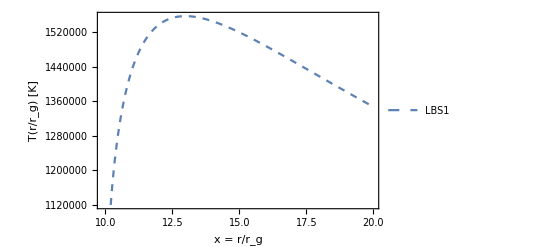

```mathematica
TLBS1=Plot[{Temp[x,14.8]},{x,9.89994,20},Frame->True,PlotStyle->Dashed,FrameLabel->{Style["x = r/r_g", Bold,13], Style["T(r/r_g) [K]", Bold, 13]},PlotLegends->{"LBS1"}]
```

```mathematica
z[x_]:= Sqrt[-gtt[x]](*Redshift*)
```

```mathematica
hp:= 6.6261*10^(-27)
```

```mathematica
kb:= 1.3807*10^(-16)
```

```mathematica
erg:=6.2415*10^(11)(* 1 erg = 6.2415 10^11 eV*)
```

```mathematica
eV := 1.6021773*10^(-12)(* 1 eV = 1.6021773 * 10^(-12) erg *)
```

```mathematica
emis[x_,ene_,M_,rmin_]:= (x*(z[x])^4)/(ⅇ^(((10^ene)*eV*z[x])/(kb*Temp[x,M,rmin]))-1)
```

```mathematica
lumi[ene_,M_,rmin_]:= NIntegrate[emis[y,ene,M,rmin],{y,9.89994,100}]

lumi[1,14.8,9.89994]
```

NIntegrate::nlim: r = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

25273.4

```mathematica
fl[ene_,M_]:= (4*π*G^2*(M*Msun)^2)/(hp^3*c^6)*(10^ene*eV)^4
```

```mathematica
lumiT[ene_,M_,rmin_]:= fl[ene,M]*lumi[ene,M,rmin]
```

```mathematica
LumiLBS1 =Plot[Log10[lumiT[ene,14,9.89994]],{ene,0,5},Frame->True,PlotRange->{25,40},FrameLabel->{Style["Log_10(E [eV])", Bold, 13],Style["Log_10(νL_ν[erg s^-1])", Bold,13]},PlotStyle->Dashed]
```

NIntegrate::nlim: r = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

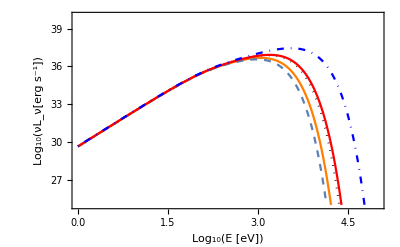

```mathematica
Show[LumiLBS2,LumiLBS1,LumiLBS3,LumiSBS1,LumiSBS2]
```

```mathematica
Show[TLBS2,TLBS1,TLBS3,TSBS1,TSBS2,TSchw,PlotRange->{1.2*10^6,2.4*10^6}]
```

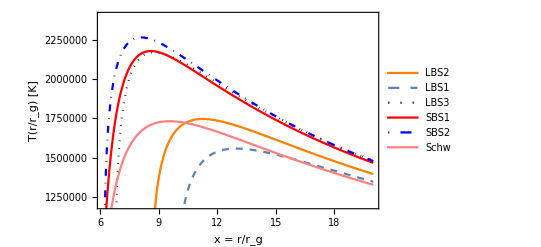

```mathematica
f[x_]:= √x+√3*(-1/2 Log[Abs[1-(√x)/(√3)]]+1/2 Log[Abs[1+(√x)/(√3)]])-(√6+√3 (-1/2 Log[-1+√2]+1/2 Log[1+√2]))
```

```mathematica
N[f[6]]
```

0.

```mathematica
Qflux[x_,M_]:= 3/2*α/M*1/x^(7/2)*1/(1-3/x)*f[x]


FSchw =Plot[Qflux[x,14.8],{x,6,20},Frame->True,FrameLabel->{Style["x = r/r_g", Bold,13], Style["Q(r/r_g) [erg cm^-2 s^-1]", Bold, 13]},PlotStyle->{Pink,Bold},PlotLegends->{"Schw"}]
```

-Graphics-

```mathematica
TS[x_,M_]:= (Qflux[x,M]/σSB)^(1/4)
```

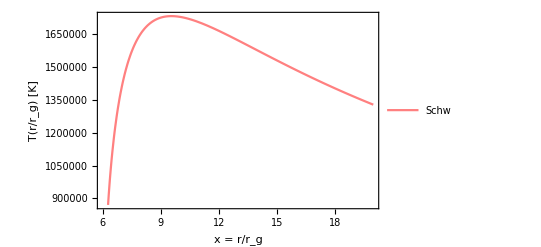

```mathematica
TSchw=Plot[TS[x,14],{x,6,20},Frame->True,PlotStyle->{Pink,Bold},FrameLabel->{Style["x = r/r_g", Bold,13], Style["T(r/r_g) [K]", Bold, 13]},PlotLegends->{"Schw"}]
```

```mathematica
Qflux[6,14]
```

1.06541×10^23

```mathematica
Show[FLBS2,FLBS1,FLBS3,FSBS1,FSBS2,FSchw,PlotRange->All]
```

-Graphics-